```mathematica
A1=(J^2-(L-S)^2)^(1/2);
A2=((L+S)^2-J^2)^(1/2);
A3=(S^2-(S1-S2)^2)^(1/2);
A4=((S1+S2)^2-S^2)^(1/2);
```

```mathematica
ξ=((J^2-L^2-S^2)(S^2(1+q)^2-(S1^2-S2^2)(1-q^2))-(1-q^2)A1 A2 A3 A4 Cos[ϕ])/(4q M^2 S^2 L)
```

((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/(4 L M^2 q S^2)

```mathematica
dξ=Simplify[D[ξ,S]]
```

-((J^2-L^2-S^2) ((1+q)^2 S^2+(-1+q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/(2 L M^2 q S^3)+1/(4 L M^2 q S^2)(-2 (1+q)^2 S^3-2 (1+q)^2 S (-J^2+L^2+S^2)-2 (-1+q^2) S (S1^2-S2^2)+((1-q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) Cos[ϕ])/(√(-S^2+(S1+S2)^2))+((-1+q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/(√(S^2-(S1-S2)^2))+((-1+q^2) √(J^2-(L-S)^2) (L+S) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/(√(-J^2+(L+S)^2))+((-1+q^2) (L-S) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/(√(J^2-(L-S)^2)))

```mathematica
rules={S->NormS[t],J->NormJ[t],L->NormL[t],S1->NormS1[t],S2->NormS2[t]};
```

```mathematica
ξ=Simplify[ξ/.rules]
dξP=Simplify[dξ/.Cos[ϕ]->-1/.rules]
dξM=Simplify[dξ/.Cos[ϕ]->+1/.rules]
```

1/(4 M^2 q NormL[t] NormS[t]^2)((-1+q^2) Cos[ϕ] √(NormJ[t]^2-(NormL[t]-NormS[t])^2) √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2)+(NormJ[t]^2-NormL[t]^2-NormS[t]^2) ((1+q)^2 NormS[t]^2+(-1+q^2) (NormS1[t]^2-NormS2[t]^2)))

-1/(4 M^2 q NormL[t] NormS[t]^3)(2 (1+q)^2 NormJ[t]^2 NormS[t]^2-2 (1+q)^2 NormL[t]^2 NormS[t]^2+2 (1+q)^2 NormS[t]^2 (-NormJ[t]^2+NormL[t]^2+NormS[t]^2)+2 (-1+q^2) NormJ[t]^2 (NormS1[t]^2-NormS2[t]^2)-2 (-1+q^2) NormL[t]^2 (NormS1[t]^2-NormS2[t]^2)-((-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) NormS[t]^2 √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2))/(√(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))+((-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) NormS[t]^2 √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))/(√(NormS[t]^2-(NormS1[t]-NormS2[t])^2))+((-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) NormS[t] (NormL[t]+NormS[t]) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))/(√(-NormJ[t]^2+(NormL[t]+NormS[t])^2))-2 (-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2)+((-1+q^2) (NormL[t]-NormS[t]) NormS[t] √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))/(√(NormJ[t]^2-(NormL[t]-NormS[t])^2)))

1/(4 M^2 q NormL[t] NormS[t]^3)(-2 (1+q)^2 NormJ[t]^2 NormS[t]^2+2 (1+q)^2 NormL[t]^2 NormS[t]^2-2 (1+q)^2 NormS[t]^2 (-NormJ[t]^2+NormL[t]^2+NormS[t]^2)-2 (-1+q^2) NormJ[t]^2 (NormS1[t]^2-NormS2[t]^2)+2 (-1+q^2) NormL[t]^2 (NormS1[t]^2-NormS2[t]^2)-((-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) NormS[t]^2 √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2))/(√(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))+((-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) NormS[t]^2 √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))/(√(NormS[t]^2-(NormS1[t]-NormS2[t])^2))+((-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) NormS[t] (NormL[t]+NormS[t]) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))/(√(-NormJ[t]^2+(NormL[t]+NormS[t])^2))-2 (-1+q^2) √(NormJ[t]^2-(NormL[t]-NormS[t])^2) √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2)+((-1+q^2) (NormL[t]-NormS[t]) NormS[t] √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2))/(√(NormJ[t]^2-(NormL[t]-NormS[t])^2)))

```mathematica
dξP2=Simplify[dξ/.Cos[ϕ]->-1/.M->1]
dξM2=Simplify[dξ/.Cos[ϕ]->+1/.M->1]
```

-1/(4 L q S^2)(2 (1+q)^2 S^3+2 (1+q)^2 S (-J^2+L^2+S^2)+2 (-1+q^2) S (S1^2-S2^2)-((-1+q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2))/(√(-S^2+(S1+S2)^2))+((-1+q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(-S^2+(S1+S2)^2))/(√(S^2-(S1-S2)^2))+((-1+q^2) √(J^2-(L-S)^2) (L+S) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(-J^2+(L+S)^2))+((-1+q^2) (L-S) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(J^2-(L-S)^2)))-((1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2)+(J^2-L^2-S^2) ((1+q)^2 S^2+(-1+q^2) (S1^2-S2^2)))/(2 L q S^3)

1/(4 L q S^2)(-2 (1+q)^2 S^3-2 (1+q)^2 S (-J^2+L^2+S^2)-2 (-1+q^2) S (S1^2-S2^2)+((1-q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2))/(√(-S^2+(S1+S2)^2))+((-1+q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(-S^2+(S1+S2)^2))/(√(S^2-(S1-S2)^2))+((-1+q^2) √(J^2-(L-S)^2) (L+S) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(-J^2+(L+S)^2))+((-1+q^2) (L-S) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(J^2-(L-S)^2)))-((-1+q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2)+(J^2-L^2-S^2) ((1+q)^2 S^2+(-1+q^2) (S1^2-S2^2)))/(2 L q S^3)

```mathematica
ξ1p=Simplify[1/(4 √a q^2 x^2)(1+q)^2 ((b^2-(a q^2)/(1+q)^4-x^2) (-((-1+q)^2 (1+q^2))/(1+q)^2+(1+q)^2 x^2)+(-1+q^2) √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(((1+q^2)^2-(1+q)^4 x^2)/(1+q)^4) √(b^2-(-(√a q)/(1+q)^2+x)^2) √(-b^2+((√a q)/(1+q)^2+x)^2) Cos[ϕ])/.Cos[ϕ]->-1]
```

((1+q)^2 ((b^2-(a q^2)/(1+q)^4-x^2) (-((-1+q)^2 (1+q^2))/(1+q)^2+(1+q)^2 x^2)-(-1+q^2) √(((1+q^2)^2)/(1+q)^4-x^2) √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(b^2-(-(√a q)/(1+q)^2+x)^2) √(-b^2+((√a q)/(1+q)^2+x)^2)))/(4 √a q^2 x^2)

```mathematica
dξ1p=Simplify[D[ξ1p,x]]
```

1/(4 √a q^2 x^3)(1+q)^2 (-(2 a (-1+q)^2 q^2 (1+q^2))/(1+q)^6+(2 b^2 (-1+q)^2 (1+q^2))/(1+q)^2+(2 a q^2 x^2)/(1+q)^2-2 b^2 (1+q)^2 x^2+2 (1+q)^2 x^2 (b^2-(a q^2)/(1+q)^4-x^2)-((-1+q^2) x ((√a q)/(1+q)^2+x) √(((1+q^2)^2)/(1+q)^4-x^2) √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(b^2-(-(√a q)/(1+q)^2+x)^2))/(√(-b^2+((√a q)/(1+q)^2+x)^2))+((-1+q^2) x (-(√a q)/(1+q)^2+x) √(((1+q^2)^2)/(1+q)^4-x^2) √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(-b^2+((√a q)/(1+q)^2+x)^2))/(√(b^2-(-(√a q)/(1+q)^2+x)^2))-((-1+q^2) x^2 √(((1+q^2)^2)/(1+q)^4-x^2) √(b^2-(-(√a q)/(1+q)^2+x)^2) √(-b^2+((√a q)/(1+q)^2+x)^2))/(√((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2))+((-1+q^2) x^2 √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(b^2-(-(√a q)/(1+q)^2+x)^2) √(-b^2+((√a q)/(1+q)^2+x)^2))/(√(((1+q^2)^2)/(1+q)^4-x^2))+2 (-1+q^2) √(((1+q^2)^2)/(1+q)^4-x^2) √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(b^2-(-(√a q)/(1+q)^2+x)^2) √(-b^2+((√a q)/(1+q)^2+x)^2))

```mathematica
q=0.6;
a=1;
b=10;
```

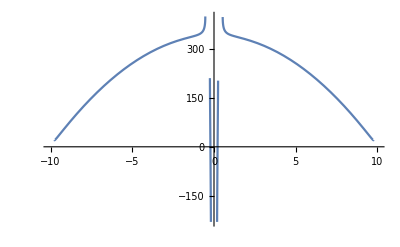

```mathematica
Plot[ξ1p,{x,-10,10}]
```

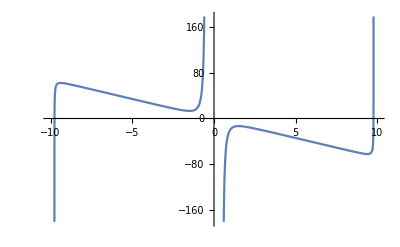

```mathematica
Plot[dξ1p,{x,-10,10}]
```